Notebook to generate the results of the paper :
  "Negative feedback may suppress variation to improve collective foraging performance"
by Andreagiovanni Reina and James A. R. Marshall
The University of Sheffield, UK
Author of the notebook: Andreagiovanni Reina, January 2020

### Plotting the ODE trajectories

#### Declaring generic layout options

```mathematica
(*******************) 
axesSize=18;
labelSize=20;
lineThickness=0.01;
legendSize=14;
legendMarkerSize=25;
colours=ColorData[97,"ColorList"];
frame[legend_]:=Framed[legend,FrameStyle->Gray,RoundingRadius->2,FrameMargins->0,Background->White]
(*******************)
```

#### Declaring the generic ODE system

```mathematica
systemND={
A'[t]==(1-A[t]-B[t]-Z[t])*Subscript[γ, a]-A[t]*α+A[t]*(1-A[t]-B[t]-Z[t])*Subscript[ρ, a]-A[t]*A[t]*Subscript[ζ, a],
B'[t]==(1-A[t]-B[t]-Z[t])*Subscript[γ, b]-B[t]*α+B[t]*(1-A[t]-B[t]-Z[t])*Subscript[ρ, b]-B[t]*B[t]*Subscript[ζ, b],
Z'[t]==(1-A[t]-B[t]-Z[t])*Subscript[γ, z]-Z[t]*α+Z[t]*(1-A[t]-B[t]-Z[t])*Subscript[ρ, z]-Z[t]*Z[t]*Subscript[ζ, z],
A[0]==startA,B[0]==startB,Z[0]==startZ};
```

#### Plotting the temporal evolution of the system without negative feedback

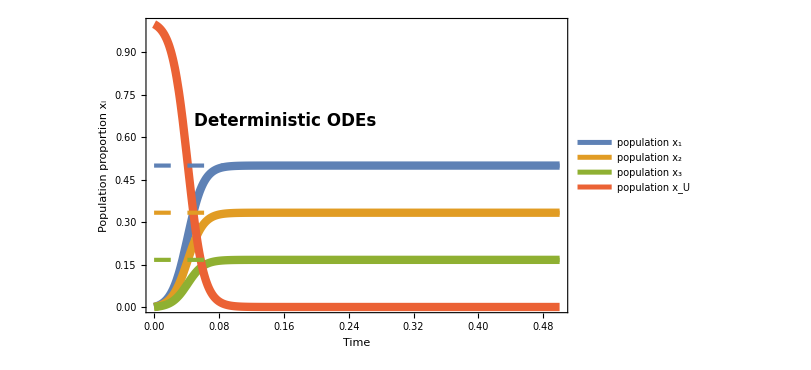

```mathematica
params={α->0.001,γ->v,Subscript[ρ, a]->r,Subscript[ρ, b]->r,Subscript[ρ, z]->r,Subscript[ζ, a]->h,Subscript[ζ, b]->h,Subscript[ζ, z]->h};
rho=100;
values={Subscript[v, a]->0.75,Subscript[v, b]->0.5,Subscript[v, z]->0.25,r->rho,h->0};
startingPoint={startA->0,startB->0,startZ->0};
tmax=0.5;
tA=Subscript[v, a]/(Subscript[v, a]+Subscript[v, b]+Subscript[v, z])/.values;
tB=Subscript[v, b]/(Subscript[v, a]+Subscript[v, b]+Subscript[v, z])/.values;
tC=Subscript[v, z]/(Subscript[v, a]+Subscript[v, b]+Subscript[v, z])/.values;
timeSol=NDSolve[systemND/.params/.values/.startingPoint,{A,B,Z},{t,0,tmax}];
odeRforInset=Show[Plot[Evaluate[{A[t],B[t],Z[t],1-(A[t]+B[t]+Z[t])}/.timeSol],{t,0,tmax},
PlotRange->{{0,tmax},{0,1}},
PlotStyle->Thickness[lineThickness],
Frame->True,
FrameLabel->{"Time","Population proportion x_i"},
FrameTicksStyle->Directive[axesSize],
FrameStyle->Directive[labelSize],
ImageSize->600,
PlotLegends->Placed[LineLegend[{"population x_1","population x_2","population x_3","population x_U"},LegendLayout->{"Row",3},LabelStyle->(legendSize)],{0.33,0.85}]
],
Graphics[{
{Directive[{Dashing[0.02],colours[[1]],Thickness[lineThickness/2]}],Line[{{0,tA},{tmax,tA}}]},
{Directive[{Dashing[0.02],colours[[2]],Thickness[lineThickness/2]}],Line[{{0,tB},{tmax,tB}}]},
{Directive[{Dashing[0.02],colours[[3]],Thickness[lineThickness/2]}],Line[{{0,tC},{tmax,tC}}]},
{Text[Style[" Deterministic ODEs ",legendSize*1.2,Bold],Scaled[{0.33,0.65}],Background->GrayLevel[0.8]]}
}]
];

startingPoint={startA->0,startB->0,startZ->0.05};
tmaxInset=250000;
timeSol=NDSolve[systemND/.params/.values/.startingPoint,{A,B,Z},{t,0,tmaxInset}];
odeRslowforInset=Show[Plot[Evaluate[{A[t],B[t],Z[t],1-(A[t]+B[t]+Z[t])}/.timeSol],{t,0,tmaxInset},
PlotRange->{{0,tmaxInset},{0,1}},
PlotStyle->Thickness[lineThickness],
Frame->True,
FrameLabel->{"",""},
FrameTicksStyle->Directive[axesSize/2],
FrameStyle->Directive[labelSize/2],
ImageSize->600,
FrameTicks->{Automatic,{Table[{n*10000,ToString[n]<>"×10^4"},{n,Range[5,20,5]}],None}}
],
Graphics[{
{Directive[{Dashing[0.02],colours[[1]],Thickness[lineThickness/2]}],Line[{{0,tA},{tmaxInset,tA}}]},
{Directive[{Dashing[0.02],colours[[2]],Thickness[lineThickness/2]}],Line[{{0,tB},{tmaxInset,tB}}]},
{Directive[{Dashing[0.02],colours[[3]],Thickness[lineThickness/2]}],Line[{{0,tC},{tmaxInset,tC}}]}
}]
];
odeRwithInset=Show[
odeRforInset,
Epilog->{
Inset[odeRslowforInset,Scaled[{0.63,0.61}],{0,0},{0.43*tmax,Automatic}]}(*Scaled[{0.63,0.61}]*)
]
```

#### Defining the iterative search algorithm to compute the best value of social inhibition for a given rho value

```mathematica
Clear[iterateSearch];

convergenceTimeBelowTargetError2[v1_,v2_,rho_,zeta_,targetError_]:=Module[{params,values,tmax,systemND,timeSol},
params={α->0.001,Subscript[γ, a]->v1,Subscript[γ, b]->v2,Subscript[ρ, a]->rho v1,Subscript[ρ, b]->rho v2,Subscript[ζ, a]->zeta,Subscript[ζ, b]->zeta};
tmax=1000;
systemND={
A'[t]==(1-A[t]-B[t])*Subscript[γ, a]-A[t]*α+A[t]*(1-A[t]-B[t])*Subscript[ρ, a]-A[t]*A[t]*Subscript[ζ, a],
B'[t]==(1-A[t]-B[t])*Subscript[γ, b]-B[t]*α+B[t]*(1-A[t]-B[t])*Subscript[ρ, b]-B[t]*B[t]*Subscript[ζ, b],
A[0]==0,B[0]==0
};
timeSol=ParametricNDSolve[systemND/.params,{A,B},{t,0,tmax},{}];
If[(Re[(A[][tmax]-v1/(v1+v2))^2+(B[][tmax]-v2/(v1+v2))^2/.timeSol])>targetError,tmax,
Quiet[Check[FindMinimum[{t,(Re[(A[][t]-v1/(v1+v2))^2+(B[][t]-v2/(v1+v2))^2/.timeSol])≤targetError,0<t≤tmax},{t,1},Method ->"InteriorPoint",MaxIterations->10^3][[1]],tmax,FindMinimum::eit]]
]
]

iterateSearch[v1_,v2_,rho_,error_,currentMin_,currentMax_,minVal_,maxVal_]:=Module[{newZ,newVal,bestZ},
sensitivity=0.001;
If[currentMax-currentMin≤sensitivity,
If[minVal≤maxVal,Return[{currentMin,minVal}],Return[{currentMax,maxVal}]]
,
newZ=currentMin+(currentMax-currentMin)0.5;
newVal=convergenceTimeBelowTargetError2[v1,v2,rho,newZ,error];
If[newVal<minVal,
Return[iterateSearch[v1,v2,rho,error,newZ,currentMax,newVal,maxVal]],
If[newVal≤maxVal,
Return[iterateSearch[v1,v2,rho,error,currentMin,newZ,minVal,newVal]],
Return[iterateSearch[v1,v2,rho,error,newZ,currentMax,newVal,maxVal]](*in case of an increase of value on both limits, I move up.*)
]]
];
]
```

#### Plotting the temporal evolution of the system with negative feedback

Zeta = 3.42712

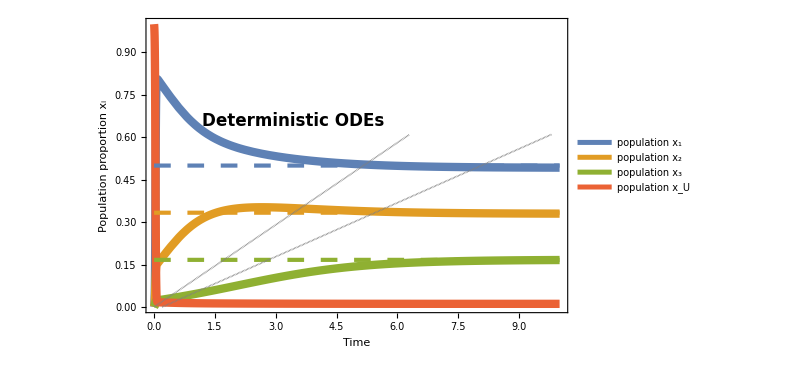

```mathematica
rho=200;
v1=0.75;v2=0.5;tmaxToFindZeta=1000;
zeta=iterateSearch[v1,v2,rho,10^-4,0,100,tmaxToFindZeta,tmaxToFindZeta][[1]];
Print["Zeta = "<>ToString[zeta]]
params={α->0.001,γ->v,Subscript[ρ, a]->r Subscript[v, a],Subscript[ρ, b]->r Subscript[v, b],Subscript[ρ, z]->r Subscript[v, z],Subscript[ζ, a]->h,Subscript[ζ, b]->h,Subscript[ζ, z]->h};
values={Subscript[v, a]->0.75,Subscript[v, b]->0.5,Subscript[v, z]->0.25,r->rho,h->zeta};
startingPoint={startA->0,startB->0,startZ->0};
tA=Subscript[v, a]/(Subscript[v, a]+Subscript[v, b]+Subscript[v, z])/.values;
tB=Subscript[v, b]/(Subscript[v, a]+Subscript[v, b]+Subscript[v, z])/.values;
tC=Subscript[v, z]/(Subscript[v, a]+Subscript[v, b]+Subscript[v, z])/.values;
tmax=10;
zoomFactor=50;
timeSol=NDSolve[systemND/.params/.values/.startingPoint,{A,B,Z},{t,0,tmax}];
odeS=Show[Plot[Evaluate[{A[t],B[t],Z[t],1-(A[t]+B[t]+Z[t])}/.timeSol],{t,0,tmax},
PlotRange->{{0,tmax},{0,1}},
PlotStyle->Thickness[lineThickness],
Frame->True,
FrameLabel->{"Time","Population proportion x_i"},
FrameTicksStyle->Directive[axesSize],
FrameStyle->Directive[labelSize],
ImageSize->600,
PlotLegends->Placed[LineLegend[{"population x_1","population x_2","population x_3","population x_U"},LegendLayout->{"Row",3},LabelStyle->legendSize],{0.35,0.85}]
],
Graphics[{
{Directive[{Dashing[0.02],colours[[1]],Thickness[lineThickness/2]}],Line[{{0,tA},{tmax,tA}}]},
{Directive[{Dashing[0.02],colours[[2]],Thickness[lineThickness/2]}],Line[{{0,tB},{tmax,tB}}]},
{Directive[{Dashing[0.02],colours[[3]],Thickness[lineThickness/2]}],Line[{{0,tC},{tmax,tC}}]},
{Directive[{Dashing[0.0],Gray,Thickness[lineThickness/5]}],Line[{{0,0},{0.63*tmax,0.61}}]},
{Directive[{Dashing[0.0],Gray,Thickness[lineThickness/5]}],Line[{{tmax/zoomFactor,0},{0.98*tmax,0.61}}]},
{Text[Style[" Deterministic ODEs ",legendSize*1.2,Bold],Scaled[{0.35,0.65}],Background->GrayLevel[0.8]]}
}]
];
odeSinset=Show[Plot[Evaluate[{A[t],B[t],Z[t],1-(A[t]+B[t]+Z[t])}/.timeSol],{t,0,tmax/zoomFactor},
PlotRange->{{0,tmax/zoomFactor},{0,1}},
PlotStyle->Thickness[lineThickness],
Frame->True,
FrameLabel->{"",""},
FrameTicksStyle->Directive[axesSize/2],
FrameStyle->Directive[labelSize/2],
ImageSize->600
(*FrameTicks->{Automatic,{Table[{n*10000,ToString[n]<>"×10^4"},{n,Range[5,20,5]}],None}}*)
],
Graphics[{
{Directive[{Dashing[0.02],colours[[1]],Thickness[lineThickness/2]}],Line[{{0,tA},{tmax,tA}}]},
{Directive[{Dashing[0.02],colours[[2]],Thickness[lineThickness/2]}],Line[{{0,tB},{tmax,tB}}]},
{Directive[{Dashing[0.02],colours[[3]],Thickness[lineThickness/2]}],Line[{{0,tC},{tmax,tC}}]}
}]
];
odeSwithInset=Show[
odeS,
Epilog->{
Inset[odeSinset,Scaled[{0.63,0.61}],{0,0},{tmax*0.43,Automatic}]}(*Scaled[{0.63,0.61}]*)
]
```

#### Plotting the temporal evolution of the system without any social feedback

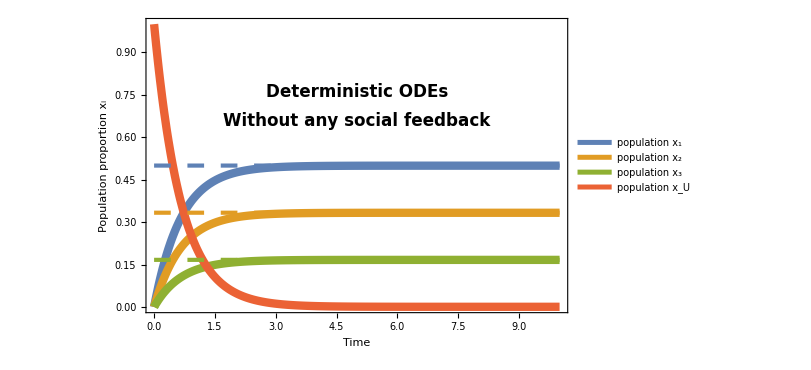

```mathematica
params={α->0.001,γ->v,Subscript[ρ, a]->r Subscript[v, a],Subscript[ρ, b]->r Subscript[v, b],Subscript[ρ, z]->r Subscript[v, z],Subscript[ζ, a]->h,Subscript[ζ, b]->h,Subscript[ζ, z]->h};
values={Subscript[v, a]->0.75,Subscript[v, b]->0.5,Subscript[v, z]->0.25,r->0,h->0};
startingPoint={startA->0,startB->0,startZ->0};
tA=Subscript[v, a]/(Subscript[v, a]+Subscript[v, b]+Subscript[v, z])/.values;
tB=Subscript[v, b]/(Subscript[v, a]+Subscript[v, b]+Subscript[v, z])/.values;
tC=Subscript[v, z]/(Subscript[v, a]+Subscript[v, b]+Subscript[v, z])/.values;
tmax=10;
timeSol=NDSolve[systemND/.params/.values/.startingPoint,{A,B,Z},{t,0,tmax}];
odeNoSoc=Show[Plot[Evaluate[{A[t],B[t],Z[t],1-(A[t]+B[t]+Z[t])}/.timeSol],{t,0,tmax},
PlotRange->{{0,tmax},{0,1}},
PlotStyle->Thickness[lineThickness],
Frame->True,
FrameLabel->{"Time","Population proportion x_i"},
FrameTicksStyle->Directive[axesSize],
FrameStyle->Directive[labelSize],
ImageSize->600,
PlotLegends->Placed[LineLegend[{"population x_1","population x_2","population x_3","population x_U"},LegendLayout->{"Row",3},LabelStyle->legendSize],{0.5,0.88}]
],
Graphics[{
{Directive[{Dashing[0.02],colours[[1]],Thickness[lineThickness/2]}],Line[{{0,tA},{tmax,tA}}]},
{Directive[{Dashing[0.02],colours[[2]],Thickness[lineThickness/2]}],Line[{{0,tB},{tmax,tB}}]},
{Directive[{Dashing[0.02],colours[[3]],Thickness[lineThickness/2]}],Line[{{0,tC},{tmax,tC}}]},
{Text[Style[" Deterministic ODEs ",legendSize*1.2,Bold],Scaled[{0.5,0.75}],Background->GrayLevel[0.8]]},
Text[Style[" Without any social feedback ",legendSize*1.2,Bold],Scaled[{0.5,0.65}],Background->RGBColor["#80d959"]]
}]
];
Print[odeNoSoc];
```

### Plotting the master equation trajectories

#### Load the raw data of the trajectories from files

```mathematica
resDir=NotebookDirectory[]<>"published_data/";
numRuns=1000;
n=3;
va=0.75;
vb=0.5;
rho=100.;
S=200; (* system size *)
evoRECa={};
evoRECb={};
evoRECc={};
evoVASIa={};
evoVASIb={};
evoVASIc={};
evoNOSOCa={};
evoNOSOCb={};
evoNOSOCc={};
Do[
rawDataVASI=Import[resDir<>"evo_N-200_g-1_r-"<>ToString[NumberForm[rho+.0,{3,1}]]<>"_n-"<>ToString[n]<>"_v-"<>ToString[NumberForm[va,{3,2}]]<>"-"<>ToString[vb]<>"_VASI_"<>ToString[run]<>".txt","Table"];
rawDataREC=Import[resDir<>"evo_N-200_g-1_r-"<>ToString[NumberForm[rho+.0,{3,1}]]<>"_n-"<>ToString[n]<>"_v-"<>ToString[NumberForm[va,{3,2}]]<>"-"<>ToString[vb]<>"_IFD_"<>ToString[run]<>".txt","Table"];
rawDataNOSOC=Import[resDir<>"evo_N-200_g-1_r-"<>ToString[NumberForm[rho+.0,{3,1}]]<>"_n-"<>ToString[n]<>"_v-"<>ToString[NumberForm[va,{3,2}]]<>"-"<>ToString[vb]<>"_NOSOC_"<>ToString[run]<>".txt","Table"];
AppendTo[evoRECa,rawDataREC[[All,{1,3}]]];
AppendTo[evoVASIa,rawDataVASI[[All,{1,3}]]];
AppendTo[evoRECb,rawDataREC[[All,{1,4}]]];
AppendTo[evoVASIb,rawDataVASI[[All,{1,4}]]];
AppendTo[evoRECc,rawDataREC[[All,{1,5}]]];
AppendTo[evoVASIc,rawDataVASI[[All,{1,5}]]];
AppendTo[evoNOSOCa,rawDataNOSOC[[All,{1,3}]]];
AppendTo[evoNOSOCb,rawDataNOSOC[[All,{1,4}]]];
AppendTo[evoNOSOCc,rawDataNOSOC[[All,{1,5}]]];
,{run,Range[0,numRuns-1,1]}]
```

#### Plotting the trajectories of the system without negative feedback

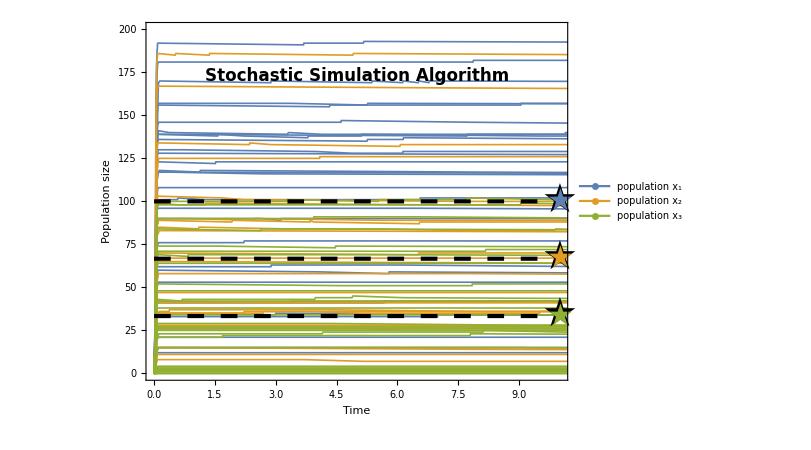

```mathematica
trajThickness=0.002;
runs=30;
wiskersRuns=1000;
tmax=10;
trjR=Show[ListPlot[evoRECa[[1;;runs]],
PlotStyle->{Directive[colours[[1]],Thickness[trajThickness]]},
Joined->True
],
ListPlot[evoRECb[[1;;runs]],
PlotStyle->{Directive[colours[[2]],Thickness[trajThickness]]},
Joined->True
],
ListPlot[evoRECc[[1;;runs]],
PlotStyle->{Directive[colours[[3]],Thickness[trajThickness]]},
Joined->True
],
Graphics[{
{Directive[{Dashing[0.02],Black,Thickness[lineThickness/2]}],Line[{{0,tA S},{tmax,tA S}}]},
{Directive[{Dashing[0.02],Black,Thickness[lineThickness/2]}],Line[{{0,tB S},{tmax,tB S}}]},
{Directive[{Dashing[0.02],Black,Thickness[lineThickness/2]}],Line[{{0,tC S},{tmax,tC S}}]},
{Text[Style[★,Directive[{Black,40}]],{tmax,tA S}]},
{Text[Style[★,Directive[{Black,40}]],{tmax,tB S}]},
{Text[Style[★,Directive[{Black,40}]],{tmax,tC S}]},
{Text[Style[★,Directive[{colours[[1]],30}]],{tmax,tA S}]},
{Text[Style[★,Directive[{colours[[2]],30}]],{tmax,tB S}]},
{Text[Style[★,Directive[{colours[[3]],30}]],{tmax,tC S}]},
{Text[Style[" Stochastic Simulation Algorithm ",legendSize*1.2,Bold],Scaled[{0.5,0.85}],Background->GrayLevel[0.8]]},
{White,Rectangle[{tmax*1.025,-1},{tmax*1.15,S+1}]}
}],
Frame->True,
FrameStyle->Directive[labelSize],
FrameTicksStyle->axesSize,
FrameLabel->{"Time","Population size"},
ChartStyle->colours[[2]],
PlotRange->{{0,tmax},{0,S}},
Epilog->{
Inset[LineLegend[colours[[{1,2,3}]],{"population x_1","population x_2","population x_3"},LegendMarkers->Graphics[{AbsoluteThickness[lineThickness*400],Line[{{-10,0},{10,0}}]}],
LabelStyle->legendSize,LegendLayout->{"Row",1},LegendFunction->frame,
LegendMarkerSize->legendMarkerSize],Scaled[{0.5,0.94}]],
Inset[Show[
BoxWhiskerChart[{evoRECa[[1;;wiskersRuns,-2,2]],evoRECb[[1;;wiskersRuns,-2,2]],evoRECc[[1;;wiskersRuns,-2,2]]},
ChartStyle->Table[Directive[{colours[[ci]],Thickness[lineThickness/2]}],{ci,1,3}],
BarSpacing->0.15
],
PlotRange->{{0,45},{0,S 0.98}},Frame->False,
AspectRatio->3/4
],{tmax,0},{-1,0},Scaled[{1,1}]]
},
PlotRangeClipping->False,
ImageSize->600,
ImagePadding->{{60,40},{49,10}},
ImageMargins->0,
AspectRatio->3/4
]
```

#### Plotting the trajectories of the system with negative feedback

```mathematica
trajThickness=0.002;
runs=30;
wiskersRuns=1000;
tmax=10;
trjS=Show[ListPlot[evoVASIa[[1;;runs]],
PlotStyle->{Directive[colours[[1]],Thickness[trajThickness]]},
Joined->True,
PlotRange->Full
],
ListPlot[evoVASIb[[1;;runs]],
PlotStyle->{Directive[colours[[2]],Thickness[trajThickness]]},
Joined->True,
PlotRange->Full
],
ListPlot[evoVASIc[[1;;runs]],
PlotStyle->{Directive[colours[[3]],Thickness[trajThickness]]},
Joined->True,
PlotRange->Full
],
Graphics[{
{Directive[{Dashing[0.02],Black,Thickness[lineThickness/2]}],Line[{{0,tA S},{tmax,tA S}}]},
{Directive[{Dashing[0.02],Black,Thickness[lineThickness/2]}],Line[{{0,tB S},{tmax,tB S}}]},
{Directive[{Dashing[0.02],Black,Thickness[lineThickness/2]}],Line[{{0,tC S},{tmax,tC S}}]},
{Text[Style[★,Directive[{Black,40}]],{tmax,tA S}]},
{Text[Style[★,Directive[{Black,40}]],{tmax,tB S}]},
{Text[Style[★,Directive[{Black,40}]],{tmax,tC S}]},
{Text[Style[★,Directive[{colours[[1]],30}]],{tmax,tA S}]},
{Text[Style[★,Directive[{colours[[2]],30}]],{tmax,tB S}]},
{Text[Style[★,Directive[{colours[[3]],30}]],{tmax,tC S}]},
{Text[Style[" Stochastic Simulation Algorithm ",legendSize*1.2,Bold],Scaled[{0.5,0.85}],Background->GrayLevel[0.8]]},
{White,Rectangle[{tmax*1.025,-1},{tmax*1.15,S+1}]}
}],
Frame->True,
FrameStyle->Directive[labelSize],
FrameTicksStyle->axesSize,
FrameLabel->{"Time","Population size"},
ChartStyle->colours[[2]],
PlotRange->{{0,tmax},{0,S}},
PlotRangeClipping->False,
Epilog->{
Inset[LineLegend[colours[[{1,2,3}]],{"population x_1","population x_2","population x_3"},LegendMarkers->Graphics[{AbsoluteThickness[lineThickness*400],Line[{{-10,0},{10,0}}]}],
LabelStyle->legendSize,LegendLayout->{"Row",1},LegendFunction->frame,
LegendMarkerSize->legendMarkerSize],Scaled[{0.5,0.94}]],
Inset[Show[
BoxWhiskerChart[{evoVASIa[[1;;wiskersRuns,-2,2]],evoVASIb[[1;;wiskersRuns,-2,2]],evoVASIc[[1;;wiskersRuns,-2,2]]},
ChartStyle->Table[Directive[{colours[[ci]],Thickness[lineThickness/2]}],{ci,1,3}],
BarSpacing->0.15
],
PlotRange->{{0,45},{0,S 0.98}},Frame->False,
AspectRatio->3/4
],{tmax,0},{-1,0},Scaled[{1,1}]]
},
ImageSize->600,
ImagePadding->{{60,40},{49,1}},
ImageMargins->0,
AspectRatio->3/4
]
```

-Graphics-

#### Plotting the trajectories of the system without any social feedback

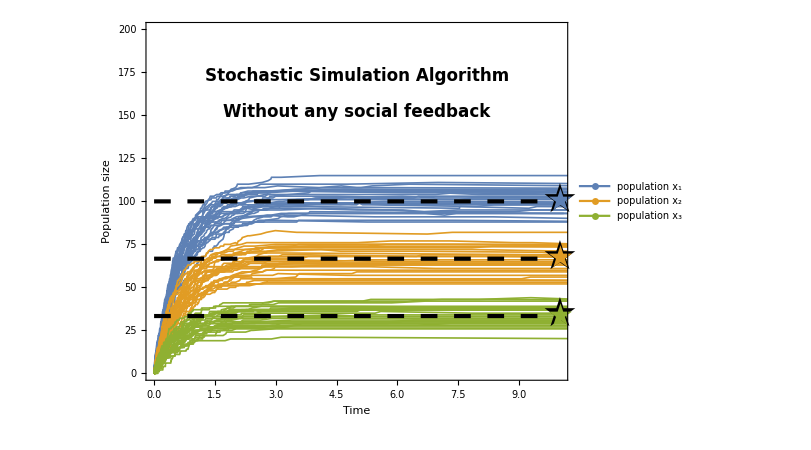

```mathematica
trajThickness=0.002;
runs=30;
wiskersRuns=1000;
tmax=10;
trjNS=Show[ListPlot[evoNOSOCa[[1;;runs]],
PlotStyle->{Directive[colours[[1]],Thickness[trajThickness]]},
Joined->True,
PlotRange->Full
],
ListPlot[evoNOSOCb[[1;;runs]],
PlotStyle->{Directive[colours[[2]],Thickness[trajThickness]]},
Joined->True,
PlotRange->Full
],
ListPlot[evoNOSOCc[[1;;runs]],
PlotStyle->{Directive[colours[[3]],Thickness[trajThickness]]},
Joined->True,
PlotRange->Full
],
Graphics[{
{Directive[{Dashing[0.02],Black,Thickness[lineThickness/2]}],Line[{{0,tA S},{tmax,tA S}}]},
{Directive[{Dashing[0.02],Black,Thickness[lineThickness/2]}],Line[{{0,tB S},{tmax,tB S}}]},
{Directive[{Dashing[0.02],Black,Thickness[lineThickness/2]}],Line[{{0,tC S},{tmax,tC S}}]},
{Text[Style[★,Directive[{Black,40}]],{tmax,tA S}]},
{Text[Style[★,Directive[{Black,40}]],{tmax,tB S}]},
{Text[Style[★,Directive[{Black,40}]],{tmax,tC S}]},
{Text[Style[★,Directive[{colours[[1]],30}]],{tmax,tA S}]},
{Text[Style[★,Directive[{colours[[2]],30}]],{tmax,tB S}]},
{Text[Style[★,Directive[{colours[[3]],30}]],{tmax,tC S}]},
{Text[Style[" Stochastic Simulation Algorithm ",legendSize*1.2,Bold],Scaled[{0.5,0.85}],Background->GrayLevel[0.8]]},
{Text[Style[" Without any social feedback ",legendSize*1.2,Bold],Scaled[{0.5,0.75}],Background->RGBColor["#80d959"]]},
{White,Rectangle[{tmax*1.025,-1},{tmax*1.15,S+1}]}
}],
Frame->True,
FrameStyle->Directive[labelSize],
FrameTicksStyle->axesSize,
FrameLabel->{"Time","Population size"},
ChartStyle->colours[[2]],
PlotRange->{{0,tmax},{0,S}},
PlotRangeClipping->False,
Epilog->{
Inset[LineLegend[colours[[{1,2,3}]],{"population x_1","population x_2","population x_3"},LegendMarkers->Graphics[{AbsoluteThickness[lineThickness*400],Line[{{-10,0},{10,0}}]}],
LabelStyle->legendSize,LegendLayout->{"Row",1},LegendFunction->frame,
LegendMarkerSize->legendMarkerSize],Scaled[{0.5,0.94}]],
Inset[Show[
BoxWhiskerChart[{evoNOSOCa[[1;;wiskersRuns,-2,2]],evoNOSOCb[[1;;wiskersRuns,-2,2]],evoNOSOCc[[1;;wiskersRuns,-2,2]]},
ChartStyle->Table[Directive[{colours[[ci]],Thickness[lineThickness/2]}],{ci,1,3}],
BarSpacing->0.15
],
PlotRange->{{0,45},{0,S 0.98}},Frame->False,
AspectRatio->3/4
],{tmax,0},{-1,0},Scaled[{1,1}]]
},
ImageSize->600,
ImagePadding->{{60,40},{49,1}},
ImageMargins->0,
AspectRatio->3/4
]
```

### Plotting the Sum of Squared Errors R^2

#### Load the raw data of the master equation runs from files

```mathematica
resDir=NotebookDirectory[]<>"published_data/";
n=2;
va=0.75;
vb=0.5;
rho=100;
S=200; (* system size *)
tA=(va/(va+vb));tB=(vb/(va+vb)); (* Targets *)
rawDataVASI=Import[resDir<>"fs_N-"<>ToString[S]<>"_g-1_r-"<>ToString[NumberForm[rho+.0,{3,1}]]<>"_n-"<>ToString[n]<>"_v-"<>ToString[NumberForm[va,{3,1}]]<>"-"<>ToString[vb]<>"_VASI.txt","Table"];
rawDataREC=Import[resDir<>"fs_N-"<>ToString[S]<>"_g-1_r-"<>ToString[NumberForm[rho+.0,{3,1}]]<>"_n-"<>ToString[n]<>"_v-"<>ToString[NumberForm[va,{3,1}]]<>"-"<>ToString[vb]<>"_IFD.txt","Table"];
```

#### Plot the R^2

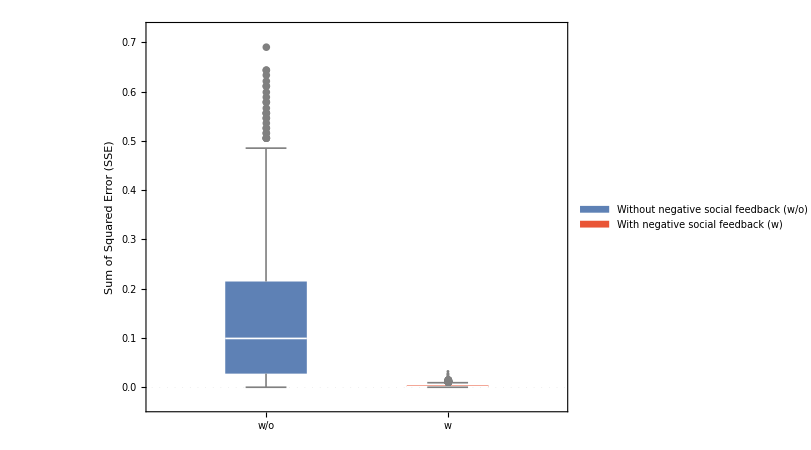

```mathematica
legendSize=16;
axesSize=18;
labelSize=20;
legendMarkerSize=16;
lineThickness=0.002;
colours=ColorData[97,"ColorList"];
frame[legend_]:=Framed[legend,FrameStyle->Gray,RoundingRadius->2,FrameMargins->0,Background->White]
barOnX=0.4;
barWidth=0.04;

plt=Show[BoxWhiskerChart[
Join[{Total[Power[rawDataREC[[All,{4,5}]]/S-ConstantArray[{tA,tB},Length[rawDataREC]],2],{2}]},
{Total[Power[rawDataVASI[[All,{4,5}]]/S-ConstantArray[{tA,tB},Length[rawDataVASI]],2],{2}]}],
{"Outliers",{"Outliers",Gray}},
ChartStyle->{Directive[{colours[[1]],Thickness[0.002]}],Directive[{colours[[11]],Thickness[0.002]}]},
ChartLabels->{{"x_1","x_2","x_U"},{"w/o","w","w/o","w","w/o","w"}},
GridLinesStyle->Directive[Dotted,Gray,Thickness[lineThickness/10]],
GridLines->{{},{0}},
FrameTicksStyle->Directive[axesSize],
FrameStyle->Directive[labelSize],
FrameLabel->{"","Sum of Squared Error (SSE)"},
ImageSize->600,
AspectRatio->3/4,
ImagePadding->{{60,1},{49,1}},
(*PlotRange->{{0.7,2.3},{0,Automatic}},*)
ImageMargins->0,
Epilog->Inset[SwatchLegend[colours[[{1,11}]],{"Without negative social feedback (w/o)","With negative social feedback (w)"},LegendFunction->frame,LabelStyle->legendSize,LegendMarkerSize->legendMarkerSize],Scaled[{0.69,0.86}]]
]
]
```

### Plotting the ODE trajectories for different starting conditions

#### Declaring the ODE systems

```mathematica
systemND={
A'[t]==(1-A[t]-B[t]-Z[t])*Subscript[γ, a]-A[t]*α+A[t]*(1-A[t]-B[t]-Z[t])*Subscript[ρ, a]-A[t]*A[t]*Subscript[ζ, a],
B'[t]==(1-A[t]-B[t]-Z[t])*Subscript[γ, b]-B[t]*α+B[t]*(1-A[t]-B[t]-Z[t])*Subscript[ρ, b]-B[t]*B[t]*Subscript[ζ, b],
Z'[t]==(1-A[t]-B[t]-Z[t])*Subscript[γ, z]-Z[t]*α+Z[t]*(1-A[t]-B[t]-Z[t])*Subscript[ρ, z]-Z[t]*Z[t]*Subscript[ζ, z],
A[0]==startA,B[0]==startB,Z[0]==startZ};
```

#### Plotting the systems starting point {0, 0.5, 0.5}

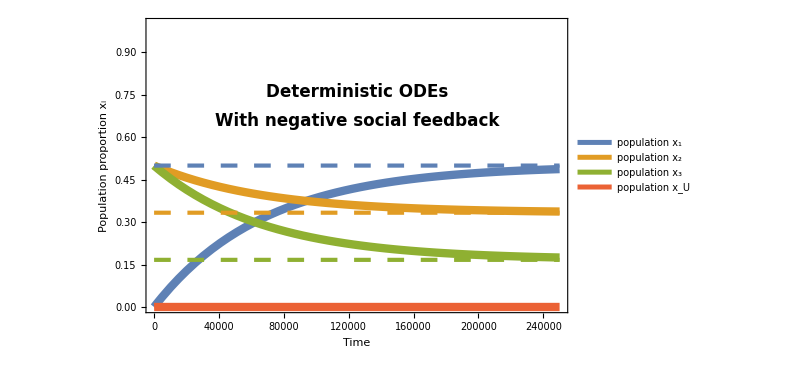

Zeta = 3.42712

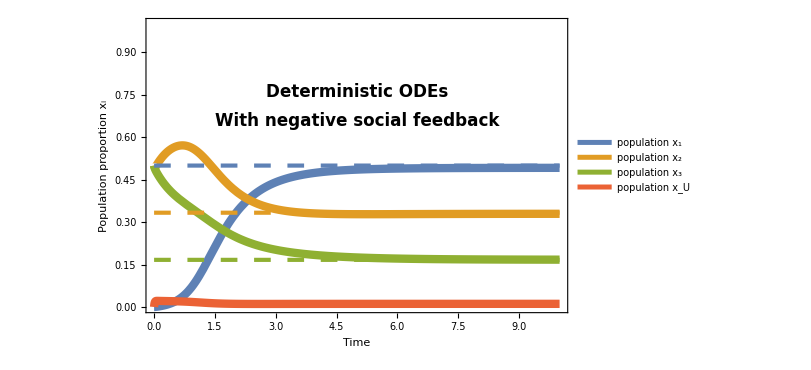

No social feedback with high abandonment α=0.01. Note the shorter time to converge.

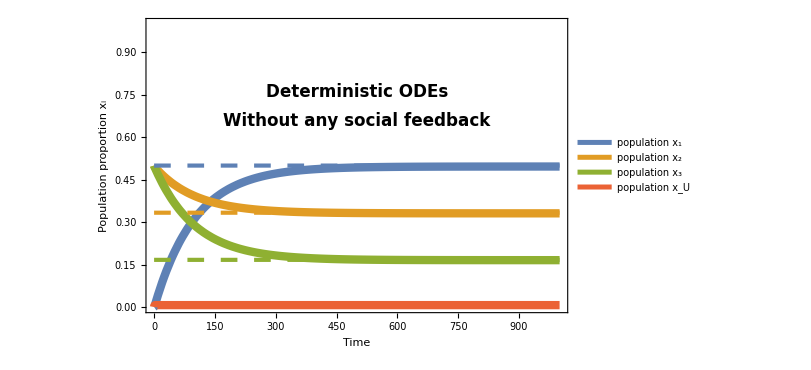

No social feedback with low abandonment α=0.001. Note the longer time to converge.

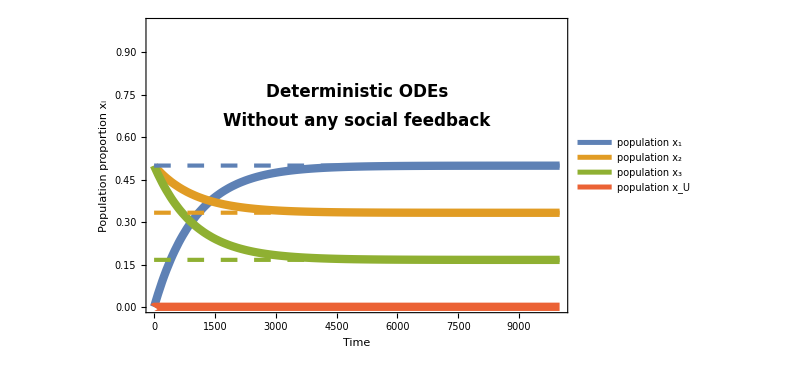

```mathematica
startingPoint={startA->0,startB->0.5,startZ->0.5};
rho=100;
params={α->0.001,γ->v,Subscript[ρ, a]->r,Subscript[ρ, b]->r,Subscript[ρ, z]->r,Subscript[ζ, a]->h,Subscript[ζ, b]->h,Subscript[ζ, z]->h};
values={Subscript[v, a]->0.75,Subscript[v, b]->0.5,Subscript[v, z]->0.25,r->rho,h->0};
tmax=250000;
tA=Subscript[v, a]/(Subscript[v, a]+Subscript[v, b]+Subscript[v, z])/.values;
tB=Subscript[v, b]/(Subscript[v, a]+Subscript[v, b]+Subscript[v, z])/.values;
tC=Subscript[v, z]/(Subscript[v, a]+Subscript[v, b]+Subscript[v, z])/.values;
timeSol=NDSolve[systemND/.params/.values/.startingPoint,{A,B,Z},{t,0,tmax}];
odeRslow=Show[Plot[Evaluate[{A[t],B[t],Z[t],1-(A[t]+B[t]+Z[t])}/.timeSol],{t,0,tmax},
PlotRange->{{0,tmax},{0,1}},
PlotStyle->Thickness[lineThickness],
Frame->True,
FrameLabel->{"Time","Population proportion x_i"},
FrameTicksStyle->Directive[axesSize],
FrameStyle->Directive[labelSize],
ImageSize->600,
PlotLegends->Placed[LineLegend[{"population x_1","population x_2","population x_3","population x_U"},LegendLayout->{"Row",3},LabelStyle->legendSize],{0.5,0.88}]
],
Graphics[{
{Directive[{Dashing[0.02],colours[[1]],Thickness[lineThickness/2]}],Line[{{0,tA},{tmax,tA}}]},
{Directive[{Dashing[0.02],colours[[2]],Thickness[lineThickness/2]}],Line[{{0,tB},{tmax,tB}}]},
{Directive[{Dashing[0.02],colours[[3]],Thickness[lineThickness/2]}],Line[{{0,tC},{tmax,tC}}]},
{Text[Style[" Deterministic ODEs ",legendSize*1.2,Bold],Scaled[{0.5,0.75}],Background->GrayLevel[0.8]]},
{Text[Style[" With negative social feedback ",legendSize*1.2,Bold],Scaled[{0.5,0.65}],Background->RGBColor["#00AEEF"]]}
}]
]

rho=rho*2;
v1=0.75;v2=0.5;tmaxToFindZeta=1000;
zeta=iterateSearch[v1,v2,rho,10^-4,0,100,tmaxToFindZeta,tmaxToFindZeta][[1]];
Print["Zeta = "<>ToString[zeta]]
params={α->0.001,γ->v,Subscript[ρ, a]->r Subscript[v, a],Subscript[ρ, b]->r Subscript[v, b],Subscript[ρ, z]->r Subscript[v, z],Subscript[ζ, a]->h,Subscript[ζ, b]->h,Subscript[ζ, z]->h};
values={Subscript[v, a]->0.75,Subscript[v, b]->0.5,Subscript[v, z]->0.25,r->rho,h->zeta};
tmax=10;
timeSol=NDSolve[systemND/.params/.values/.startingPoint,{A,B,Z},{t,0,tmax}];
odeSslow=Show[Plot[Evaluate[{A[t],B[t],Z[t],1-(A[t]+B[t]+Z[t])}/.timeSol],{t,0,tmax},
PlotRange->{{0,tmax},{0,1}},
PlotStyle->Thickness[lineThickness],
Frame->True,
FrameLabel->{"Time","Population proportion x_i"},
FrameTicksStyle->Directive[axesSize],
FrameStyle->Directive[labelSize],
ImageSize->600,
PlotLegends->Placed[LineLegend[{"population x_1","population x_2","population x_3","population x_U"},LegendLayout->{"Row",3},LabelStyle->legendSize],{0.5,0.88}]
],
Graphics[{
{Directive[{Dashing[0.02],colours[[1]],Thickness[lineThickness/2]}],Line[{{0,tA},{tmax,tA}}]},
{Directive[{Dashing[0.02],colours[[2]],Thickness[lineThickness/2]}],Line[{{0,tB},{tmax,tB}}]},
{Directive[{Dashing[0.02],colours[[3]],Thickness[lineThickness/2]}],Line[{{0,tC},{tmax,tC}}]},
{Text[Style[" Deterministic ODEs ",legendSize*1.2,Bold],Scaled[{0.5,0.75}],Background->GrayLevel[0.8]]},
{Text[Style[" With negative social feedback ",legendSize*1.2,Bold],Scaled[{0.5,0.65}],Background->RGBColor["#ed363d"]]}
}]
]

Do[
params={α->alpha,γ->v,Subscript[ρ, a]->r Subscript[v, a],Subscript[ρ, b]->r Subscript[v, b],Subscript[ρ, z]->r Subscript[v, z],Subscript[ζ, a]->h,Subscript[ζ, b]->h,Subscript[ζ, z]->h};
values={Subscript[v, a]->0.75,Subscript[v, b]->0.5,Subscript[v, z]->0.25,r->0,h->0};
tmax=10/alpha;
timeSol=NDSolve[systemND/.params/.values/.startingPoint,{A,B,Z},{t,0,tmax}];
odeNSslow=Show[Plot[Evaluate[{A[t],B[t],Z[t],1-(A[t]+B[t]+Z[t])}/.timeSol],{t,0,tmax},
PlotRange->{{0,tmax},{0,1}},
PlotStyle->Thickness[lineThickness],
Frame->True,
FrameLabel->{"Time","Population proportion x_i"},
FrameTicksStyle->Directive[axesSize],
FrameStyle->Directive[labelSize],
ImageSize->600,
PlotLegends->Placed[LineLegend[{"population x_1","population x_2","population x_3","population x_U"},LegendLayout->{"Row",3},LabelStyle->legendSize],{0.5,0.88}]
],
Graphics[{
{Directive[{Dashing[0.02],colours[[1]],Thickness[lineThickness/2]}],Line[{{0,tA},{tmax,tA}}]},
{Directive[{Dashing[0.02],colours[[2]],Thickness[lineThickness/2]}],Line[{{0,tB},{tmax,tB}}]},
{Directive[{Dashing[0.02],colours[[3]],Thickness[lineThickness/2]}],Line[{{0,tC},{tmax,tC}}]},
{Text[Style[" Deterministic ODEs ",legendSize*1.2,Bold],Scaled[{0.5,0.75}],Background->GrayLevel[0.8]]},
{Text[Style[" Without any social feedback ",legendSize*1.2,Bold],Scaled[{0.5,0.65}],Background->RGBColor["#80d959"]]}
}]
];
If[alpha==0.001,
Print["No social feedback with low abandonment α="<>ToString[alpha]<>". Note the longer time to converge."],
Print["No social feedback with high abandonment α="<>ToString[alpha]<>". Note the shorter time to converge."]
];
Print[odeNSslow];
,{alpha,{0.01,0.001}}]
```

### Speed-robustness trade-off

#### I plot the relationship between zeta and time. Thus, I compute the convergence time for a given error spanning over the zetas in my range of interest

Defining the functions

```mathematica
errorFromBinaryIdeal[v1_,v2_,rho_,zeta_]:=Module[{params,values,tmax,systemND,timeSol},
params={α->0.001,γ->v,Subscript[ρ, a]->r Subscript[v, a],Subscript[ρ, b]->r Subscript[v, b],Subscript[ζ, a]->h,Subscript[ζ, b]->h};
tmax=10000;
systemND={
A'[t]==(1-A[t]-B[t])*Subscript[γ, a]-A[t]*α+A[t]*(1-A[t]-B[t])*Subscript[ρ, a]-A[t]*A[t]*Subscript[ζ, a],
B'[t]==(1-A[t]-B[t])*Subscript[γ, b]-B[t]*α+B[t]*(1-A[t]-B[t])*Subscript[ρ, b]-B[t]*B[t]*Subscript[ζ, b],
A[0]==0,B[0]==0
};
timeSol=ParametricNDSolve[systemND/.params,{A,B,Z,W},{t,0,tmax},{Subscript[v, a],Subscript[v, b],r,h}];
Re[(A[v1,v2,rho,zeta][tmax]-v1/(v1+v2))^2+(B[v1,v2,rho,zeta][tmax]-v2/(v1+v2))^2/.timeSol]
]
convergenceTimeToItsFixedPointBelowError[v1_,v2_,rho_,zeta_,targetError_]:=Module[{params,values,tmax,systemND,timeSol,fpA,fpB},
params={α->0.001,Subscript[γ, a]->v1,Subscript[γ, b]->v2,Subscript[ρ, a]->rho v1,Subscript[ρ, b]->rho v2,Subscript[ζ, a]->zeta,Subscript[ζ, b]->zeta};
tmax=10000;
systemND={
A'[t]==(1-A[t]-B[t])*Subscript[γ, a]-A[t]*α+A[t]*(1-A[t]-B[t])*Subscript[ρ, a]-A[t]*A[t]*Subscript[ζ, a],
B'[t]==(1-A[t]-B[t])*Subscript[γ, b]-B[t]*α+B[t]*(1-A[t]-B[t])*Subscript[ρ, b]-B[t]*B[t]*Subscript[ζ, b],
A[0]==0,B[0]==0
};
timeSol=ParametricNDSolve[systemND/.params,{A,B},{t,0,tmax},{}];
(*Quiet[Check[FindMinimum[{t,(Re[(A[][t]-v1/(v1+v2))^2+(B[][t]-v2/(v1+v2))^2/.timeSol])≤targetError,0<t≤tmax},{t,1},Method ->"InteriorPoint",MaxIterations->10^3][[1]],tmax,FindMinimum::eit]]*)
(*NMinimize[{t,(Re[(A[][t]-v1/(v1+v2))^2+(B[][t]-v2/(v1+v2))^2/.timeSol])≤targetError,0<t≤tmax},t,MaxIterations->10^3][[1]]*)
fpA=A[][tmax]/.timeSol;
fpB=B[][tmax]/.timeSol;
(*Quiet[Check[*)FindMinimum[{t,(Re[(A[][t]-fpA)^2+(B[][t]-fpB)^2/.timeSol])≤targetError,0<t≤tmax},{t,1},Method ->"InteriorPoint",MaxIterations->10^3][[1]]
(*,tmax,FindMinimum::eit]]*)
]
```

Computing the data

```mathematica
v1 =0.75;
v2=0.5;
targetError=10^-4;
rho=200;
timeOnZeta=Table[{zeta,convergenceTimeToItsFixedPointBelowError[v1,v2,rho,zeta,targetError]},{zeta,Range[0.05,5,0.05]}];
errorOnZeta=Table[{zeta,errorFromBinaryIdeal[v1,v2,rho,zeta]},{zeta,Range[0.05,5,0.05]}];
```

Plotting the data

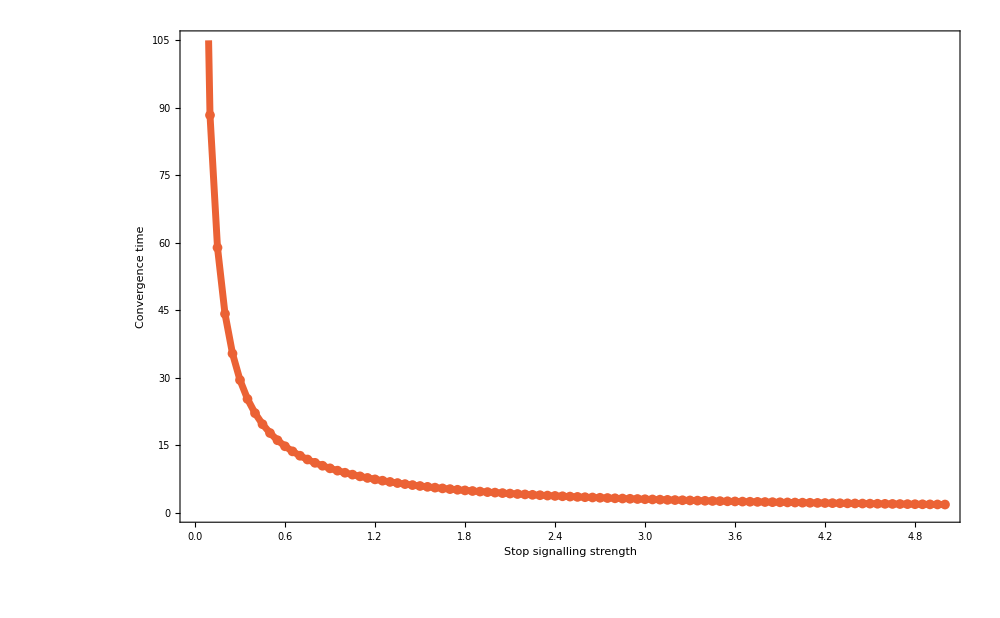
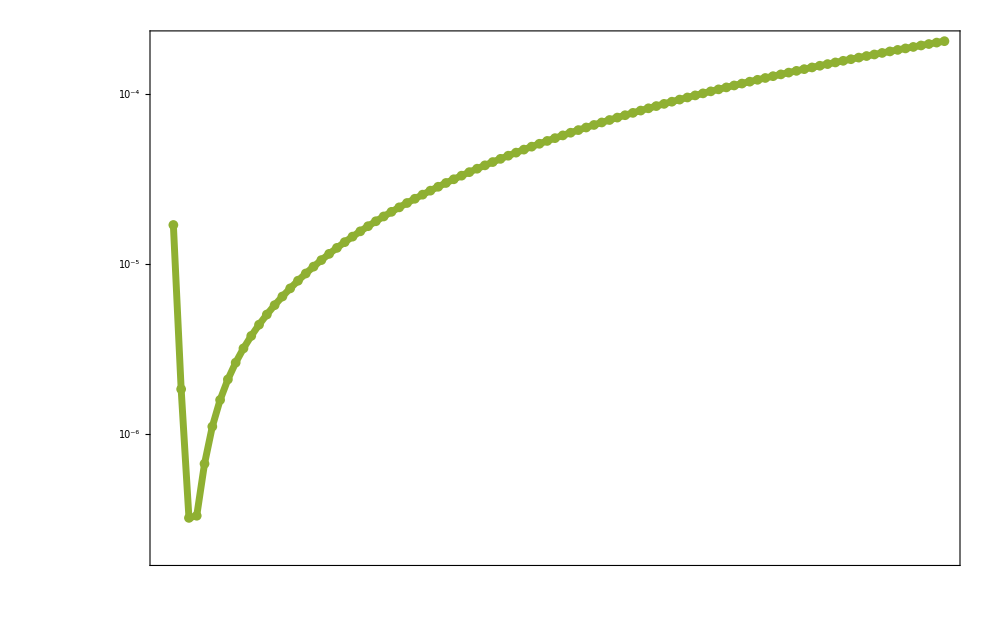

```mathematica
frameThickness=0.003;
tmax=10000;
pltLeft=ListPlot[Select[timeOnZeta,#[[2]]<tmax&],
Frame->{True,True,True,False},
PlotStyle->Directive[{Thickness[lineThickness/2],colours[[4]]}],
PlotMarkers->{Automatic,10},
FrameLabel->{"Stop signalling strength","Convergence time"},
PlotRange->{{0,Max[timeOnZeta[[All,1]]]},{0,105}},
FrameTicksStyle->Directive[axesSize],
ImageSize->1000,
ImagePadding->150,
Joined->True,
FrameStyle->{Directive[{labelSize,GrayLevel[0.25],Thickness[frameThickness]}],Directive[{labelSize,colours[[4]],Thickness[frameThickness]}],Directive[{GrayLevel[0.25],Thickness[frameThickness]}],None}
];
maxZ=Select[timeOnZeta,#[[2]]<1000&][[-1,1]];
pltRight=ListLogPlot[errorOnZeta,
Axes->False,
Frame->{False,False,False,True},
FrameTicks->{{None,All},{None,None}},
PlotStyle->Directive[{Thickness[lineThickness/2],colours[[3]]}],
PlotMarkers->{Automatic,10},
FrameLabel->{{None,"Error"},{None,None}},
PlotRange->{{0,Max[timeOnZeta[[All,1]]]},{Full,Full}},
FrameTicksStyle->Directive[axesSize],
ImageSize->1000,
ImagePadding->150,
Joined->True,
FrameStyle->{Automatic,Automatic,Automatic,Directive[{labelSize,colours[[3]],Thickness[frameThickness]}]}
];
Select[errorOnZeta,#[[2]]≥targetError&];
plt=Overlay[{pltLeft,pltRight},FrameMargins->{{-85,-50},{-98,-150}}]
```

### Computing the best social inhibition value for each value of positive social feedback and food quality

#### We fix the target error to a give value, in our case 10^-4, and run the iterative search for a large number of values of ρ and v_1

```mathematica
targetError=10^-4;
tmax=1000;
rhoZetaVs=Table[Join[{rho,N[Round[va,10^-6]],N[Round[vb,10^-6]]},iterateSearch[va,vb,rho,targetError,0,100,tmax,tmax]],{rho,Join[{1},Range[10,400,10]]},{va,Join[{0.75},Drop[Range[0.1,1.0,0.1],{5}]]},{vb,{0.5}}];
```

#### We store the computed values in a file to have quick access to them

```mathematica
Export[NotebookDirectory[]<>"published_data/computed_bestZeta.txt",Flatten[rhoZetaVs,2],"Table"];
```

```mathematica
rhoZetaVs=Import[NotebookDirectory[]<>"published_data/computed_bestZeta.txt","Table"];
```

#### Plotting a 3D surface for varying positive feedback (ρ) and food quality (q_1)

```mathematica
ListPlot3D[rhoZetaVs[[All,{1,2,4}]],AxesLabel->{"ρ","q_1","z"},AxesStyle->labelSize,TicksStyle->Directive[axesSize],ImageSize->600]
```

### Plotting the variance for varying positive feedback strength, food quality, and swarm size

#### Load the raw data of the master equation runs from files

```mathematica
resDir=NotebookDirectory[]<>"published_data/";
n=2;
vb=0.5;
variances={};
Do[Do[Do[
tA=(va/(va+vb));tB=(vb/(va+vb)); (* Targets *)
rawDataVASI=Import[resDir<>"fs_N-"<>ToString[S]<>"_g-1_r-"<>ToString[NumberForm[rho+.0,{3,1}]]<>"_n-"<>ToString[n]<>"_v-"<>ToString[NumberForm[va,{3,1}]]<>"-"<>ToString[vb]<>"_VASI.txt","Table"];
rawDataREC=Import[resDir<>"fs_N-"<>ToString[S]<>"_g-1_r-"<>ToString[NumberForm[rho+.0,{3,1}]]<>"_n-"<>ToString[n]<>"_v-"<>ToString[NumberForm[va,{3,1}]]<>"-"<>ToString[vb]<>"_IFD.txt","Table"];
varREC=N[Total[Variance[rawDataREC[[All,{4,5}]]/S]]+Covariance[Flatten[rawDataREC[[All,{4}]]/S],Flatten[rawDataREC[[All,{5}]]/S]]];
varVASI=N[Total[Variance[rawDataVASI[[All,{4,5}]]/S]]+Covariance[Flatten[rawDataVASI[[All,{4}]]/S],Flatten[rawDataVASI[[All,{5}]]/S]]];
AppendTo[variances,{rho,va,S,varREC/varVASI,varREC,varVASI,Mean[Flatten[deviationREC]],Mean[Flatten[deviationVASI]],StandardDeviation[Flatten[deviationREC]],StandardDeviation[Flatten[deviationVASI]]}];
,{va,Range[0.2,1,0.1]}],{rho,Range[10,200,10]}],{S,{50,100,200,500,750,1000}}]
```

#### Plotting the ratio of the variances for varying positive feedback strength and food quality

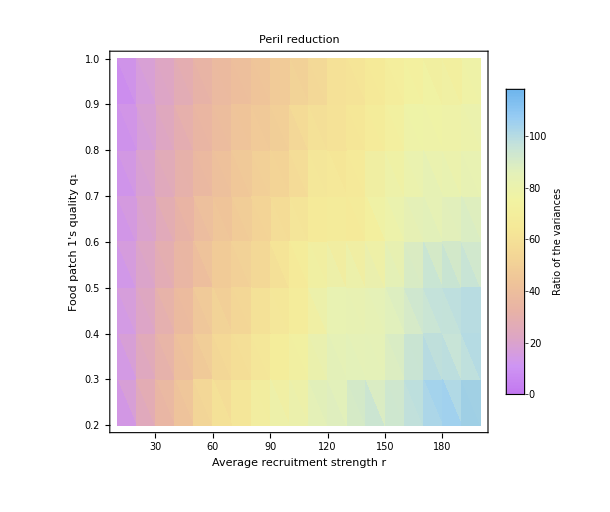

```mathematica
S=200;
colorScheme=ColorData[{"Pastel",{0,Max[Select[variances,#[[3]]==S&][[All,4]]]}}];
imageSize=512;
imageResolutionDpi=350; (*700*)
legendSize=22;
titleSize=22;
axesSize=18;
labelSize=22;

plt=ListDensityPlot[Select[variances,#[[3]]==S&][[All,{1,2,4}]],
(*InterpolationOrder->1,*)
PlotLegends->Placed[
BarLegend[{colorScheme,{0,Max[Select[variances,#[[3]]==S&][[All,4]]]}},
LegendMargins->{{0,0},{10,5}},
LegendLabel->"Ratio of the\nvariances",
LabelStyle->{Italic,Gray,FontFamily->"Helvetica",legendSize}],
Right],
FrameLabel->{"Average recruitment strength r","Food patch 1's quality q_1"},
ClippingStyle->Black,
FrameStyle->labelSize,
FrameTicksStyle->axesSize,
PlotRangePadding->0,
ColorFunction->colorScheme,
ColorFunctionScaling->False,
PlotLabel->"Peril reduction",
LabelStyle->titleSize,
PlotRange->Full,
ImageSize->imageSize
]
```

#### Plot the individual variances for the two models

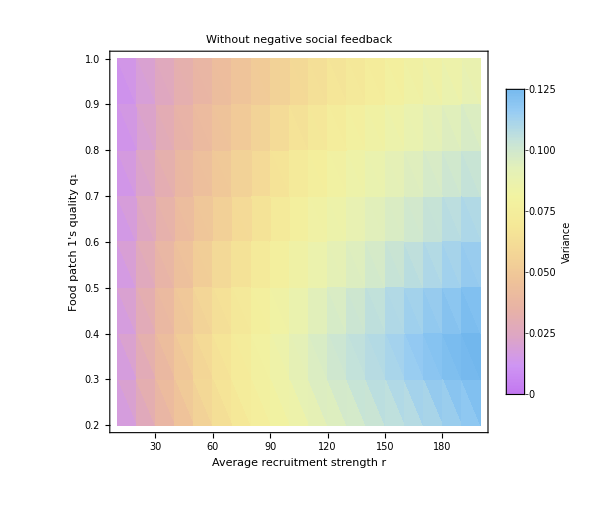
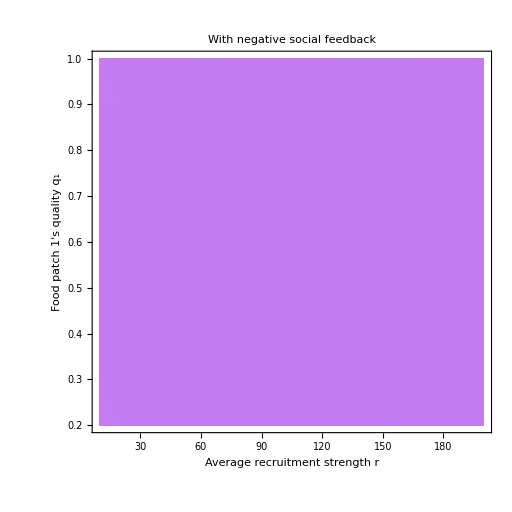
-Graphics- | -Graphics-

```mathematica
S=200;
colorScheme=ColorData[{"Pastel",{0,Max[Select[variances,#[[3]]==S&][[All,{5,6}]]]}}];
imageSize=512;
imageResolutionDpi=350; (*700*)
legendSize=22;
titleSize=22;
axesSize=18;
labelSize=22;

plt1=ListDensityPlot[Select[variances,#[[3]]==S&][[All,{1,2,5}]],
(*InterpolationOrder->1,*)
PlotLegends->Placed[
BarLegend[{colorScheme,{0,Max[Select[variances,#[[3]]==S&][[All,{5,6}]]]}},
LegendMargins->{{0,0},{10,5}},
LegendLabel->"Variance",
LabelStyle->{Italic,Gray,FontFamily->"Helvetica",legendSize}],
Right],
FrameLabel->{"Average recruitment strength r","Food patch 1's quality q_1"},
ClippingStyle->Black,
FrameStyle->labelSize,
FrameTicksStyle->axesSize,
PlotRangePadding->0,
ColorFunction->colorScheme,
ColorFunctionScaling->False,
PlotLabel->"Without negative\nsocial feedback",
LabelStyle->titleSize,
PlotRange->Full,
ImageSize->imageSize
];

plt2=ListDensityPlot[Select[variances,#[[3]]==S&][[All,{1,2,6}]],
FrameLabel->{"Average recruitment strength r","Food patch 1's quality q_1"},
ClippingStyle->Black,
FrameStyle->labelSize,
FrameTicksStyle->axesSize,
PlotRangePadding->0,
ColorFunction->colorScheme,
ColorFunctionScaling->False,
PlotLabel->"With negative\nsocial feedback",
LabelStyle->titleSize,
PlotRange->Full,
ImageSize->imageSize
];
Grid[{{plt1,plt2}}]
```

#### Plot the variances for varying positive feedback strength and swarm size

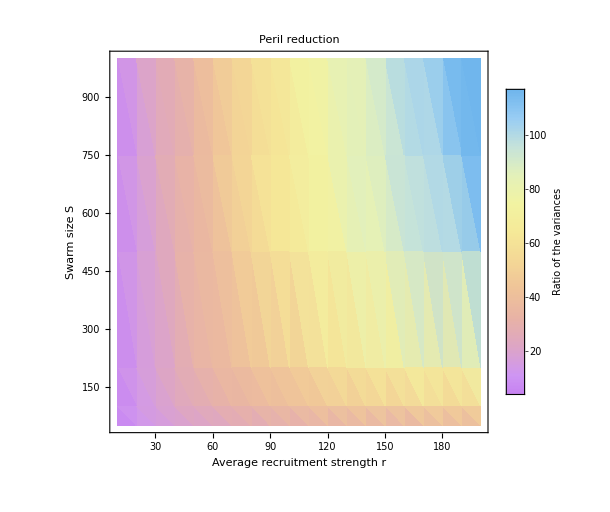

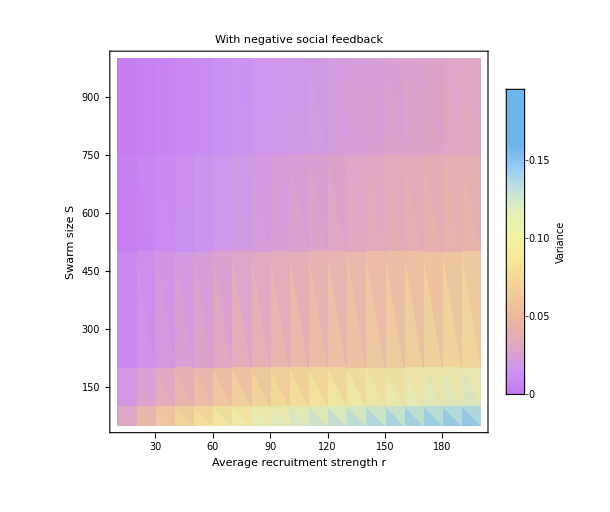

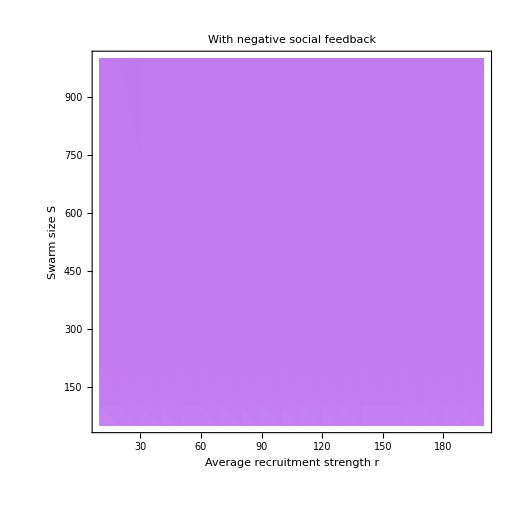

```mathematica
va=1.;
colorScheme=ColorData[{"Pastel",{0,Max[Select[variances,#[[2]]==va&][[All,4]]]}}];
imageSize=512;
imageResolutionDpi=350; (*700*)
legendSize=22;
axesSize=18;
labelSize=22;

plt=ListDensityPlot[Select[variances,#[[2]]==va&][[All,{1,3,4}]],
(*InterpolationOrder->1,*)
PlotLegends->Placed[
BarLegend[Automatic,
LegendMargins->{{0,0},{10,5}},
LegendLabel->"Ratio of the\nvariances",
LabelStyle->{Italic,Gray,FontFamily->"Helvetica",legendSize}],
Right],
FrameLabel->{"Average recruitment strength r","Swarm size S"},
ClippingStyle->Black,
FrameStyle->labelSize,
FrameTicksStyle->axesSize,
PlotRangePadding->0,
(*Mesh->{Length[Union[subset[[All,5]]]]-1,Length[Union[subset[[All,6]]]]-1},*)
ColorFunction->colorScheme,
ColorFunctionScaling->False,
(*RegionFunction->Function[{x,y,z},z>0],*)
PlotLabel->"Peril reduction",
LabelStyle->titleSize,
PlotRange->Full,
ImageSize->imageSize
]

colorScheme=ColorData[{"Pastel",{0,Max[Select[variances,#[[2]]==va&][[All,{5,6}]]]}}];
plt1=ListDensityPlot[Select[variances,#[[2]]==va&][[All,{1,3,5}]],
(*InterpolationOrder->1,*)
PlotLegends->Placed[
BarLegend[{colorScheme,{0,Max[variances[[All,{5,6}]]]}},
LegendMargins->{{0,0},{10,5}},
LegendLabel->"Variance",
LabelStyle->{Italic,Gray,FontFamily->"Helvetica",legendSize}],
Right],
FrameLabel->{"Average recruitment strength r","Swarm size S"},
ClippingStyle->Black,
FrameStyle->labelSize,
FrameTicksStyle->axesSize,
PlotRangePadding->0,
(*Mesh->{Length[Union[subset[[All,5]]]]-1,Length[Union[subset[[All,6]]]]-1},*)
ColorFunction->colorScheme,
ColorFunctionScaling->False,
(*RegionFunction->Function[{x,y,z},z>0],*)
PlotLabel->"With negative\nsocial feedback",
LabelStyle->titleSize,
PlotRange->Full,
ImageSize->imageSize
]

va=1.;
plt2=ListDensityPlot[Select[variances,#[[2]]==va&][[All,{1,3,6}]],
FrameLabel->{"Average recruitment strength r","Swarm size S"},
ClippingStyle->Black,
FrameStyle->labelSize,
FrameTicksStyle->axesSize,
PlotRangePadding->0,
(*Mesh->{Length[Union[subset[[All,5]]]]-1,Length[Union[subset[[All,6]]]]-1},*)
ColorFunction->colorScheme,
ColorFunctionScaling->False,
(*RegionFunction->Function[{x,y,z},z>0],*)
PlotLabel->"With negative\nsocial feedback",
LabelStyle->titleSize,
PlotRange->Full,
ImageSize->imageSize
]
```

### Plot peril of large deviations

#### Load the raw data of the master equation runs from files

```mathematica
resDir=NotebookDirectory[]<>"published_data/";
n=2;
vb=0.5;
S=200; (* system size *)
rho=100;
marginsTable={};
Do[Do[
tA=(va/(va+vb));tB=(vb/(va+vb)); (* Targets *)
rawDataVASI=Import[resDir<>"fs_N-200_g-1_r-"<>ToString[NumberForm[rho+.0,{3,1}]]<>"_n-"<>ToString[n]<>"_v-"<>ToString[NumberForm[va,{3,1}]]<>"-"<>ToString[vb]<>"_VASI.txt","Table"];
rawDataREC=Import[resDir<>"fs_N-200_g-1_r-"<>ToString[NumberForm[rho+.0,{3,1}]]<>"_n-"<>ToString[n]<>"_v-"<>ToString[NumberForm[va,{3,1}]]<>"-"<>ToString[vb]<>"_IFD.txt","Table"];
(* compare the maximum deviation (absolute value) from the reference value with a acceptable proportion (deviation margin) *)
deviationREC=Join[Transpose[{Abs[rawDataREC[[All,4]]/S-tA]}],Transpose[{Abs[rawDataREC[[All,5]]/S-tB]}],2];
outliersREC=Dimensions[Select[deviationREC,Max[#]>margin&]][[1]];
deviationVASI=Join[Transpose[{Abs[rawDataVASI[[All,4]]/S-tA]}],Transpose[{Abs[rawDataVASI[[All,5]]/S-tB]}],2];
outliersVASI=Dimensions[Select[deviationVASI,Max[#]>margin&]][[1]];
AppendTo[marginsTable,{rho,va,margin,outliersREC,outliersVASI,Mean[Flatten[deviationREC]],Mean[Flatten[deviationVASI]],StandardDeviation[Flatten[deviationREC]],StandardDeviation[Flatten[deviationVASI]]}];
,{va,Range[0.2,1,0.1]}],{margin,Range[0.01,0.2,0.01]}]

margin=0.1; (* outliers cutoff *)
marginFixed={};
Do[Do[
tA=(va/(va+vb));tB=(vb/(va+vb)); (* Targets *)
rawDataVASI=Import[resDir<>"fs_N-200_g-1_r-"<>ToString[NumberForm[rho+.0,{3,1}]]<>"_n-"<>ToString[n]<>"_v-"<>ToString[NumberForm[va,{3,1}]]<>"-"<>ToString[vb]<>"_VASI.txt","Table"];
rawDataREC=Import[resDir<>"fs_N-200_g-1_r-"<>ToString[NumberForm[rho+.0,{3,1}]]<>"_n-"<>ToString[n]<>"_v-"<>ToString[NumberForm[va,{3,1}]]<>"-"<>ToString[vb]<>"_IFD.txt","Table"];
(* compare the maximum deviation (absolute value) from the reference value with a acceptable proportion (deviation margin) *)
deviationREC=Join[Transpose[{Abs[rawDataREC[[All,4]]/S-tA]}],Transpose[{Abs[rawDataREC[[All,5]]/S-tB]}],2];
outliersREC=Dimensions[Select[deviationREC,Max[#]>margin&]][[1]];
deviationVASI=Join[Transpose[{Abs[rawDataVASI[[All,4]]/S-tA]}],Transpose[{Abs[rawDataVASI[[All,5]]/S-tB]}],2];
outliersVASI=Dimensions[Select[deviationVASI,Max[#]>margin&]][[1]];
AppendTo[marginFixed,{rho,va,outliersREC,outliersVASI}];
,{va,Drop[Range[0.1,1,0.1],{1}]}],{rho,Range[10,200,10]}]
```

#### Plot deviation larger than 10 % of the system size

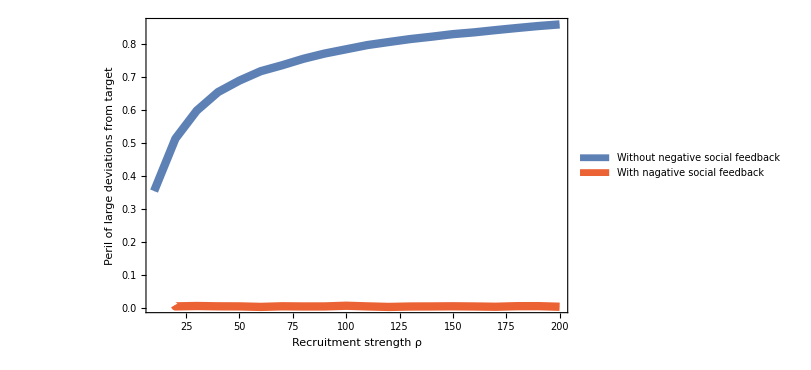

```mathematica
legendSize=20;
axesSize=18;
labelSize=20;

margin=0.1; (* outliers cutoff *)
runs=1000;
plt=Show[ListPlot[
{Join[Transpose[{Range[10,200,10]}],Transpose[{Mean[Transpose[Table[Select[marginFixed,#[[1]]==rho&][[All,3]]/runs,{rho,10,200,10}]]]}],2],
Join[Transpose[{Range[10,200,10]}],Transpose[{Mean[Transpose[Table[Select[marginFixed,#[[1]]==rho&][[All,3]]/runs,{rho,10,200,10}]]]-1.96StandardDeviation[Transpose[Table[Select[marginFixed,#[[1]]==rho&][[All,3]],{rho,10,200,10}]]/runs]/Sqrt[runs]}],2],
Join[Transpose[{Range[10,200,10]}],Transpose[{Mean[Transpose[Table[Select[marginFixed,#[[1]]==rho&][[All,3]]/runs,{rho,10,200,10}]]]+1.96StandardDeviation[Transpose[Table[Select[marginFixed,#[[1]]==rho&][[All,3]],{rho,10,200,10}]]/runs]/Sqrt[runs]}],2]}
,
PlotStyle->{Directive[colours[[1]],Thickness[0.01]],Directive[colours[[1]],Thickness[0.0]],Directive[colours[[1]],Thickness[0.0]]},
Joined->True,
Filling->{{1->{2}},{1->{3}}}
],
ListPlot[
{Join[Transpose[{Range[10,200,10]}],Transpose[{Mean[Transpose[Table[Select[marginFixed,#[[1]]==rho&][[All,4]]/runs,{rho,10,200,10}]]]}],2],
Join[Transpose[{Range[10,200,10]}],Transpose[{Mean[Transpose[Table[Select[marginFixed,#[[1]]==rho&][[All,4]]/runs,{rho,10,200,10}]]]-1.96StandardDeviation[Transpose[Table[Select[marginFixed,#[[1]]==rho&][[All,4]],{rho,10,200,10}]]/runs]/Sqrt[runs]}],2],
Join[Transpose[{Range[10,200,10]}],Transpose[{Mean[Transpose[Table[Select[marginFixed,#[[1]]==rho&][[All,4]]/runs,{rho,10,200,10}]]]+1.96StandardDeviation[Transpose[Table[Select[marginFixed,#[[1]]==rho&][[All,4]],{rho,10,200,10}]]/runs]/Sqrt[runs]}],2]}
,
PlotStyle->{Directive[colours[[4]],Thickness[0.01]],Directive[colours[[4]],Thickness[0.0]],Directive[colours[[4]],Thickness[0.0]]},
Joined->True,
Filling->{{1->{2}},{1->{3}}}
],
PlotRange->Automatic,
Frame->True,
FrameStyle->Directive[labelSize],
FrameTicksStyle->axesSize,
FrameLabel->{"Recruitment strength ρ","Peril of large deviations from target"},
ChartStyle->colours[[2]],
Epilog->Inset[SwatchLegend[{colours[[1]],colours[[4]]},{"Without negative social feedback","With nagative social feedback"},LegendFunction->frame,LabelStyle->legendSize,LegendMarkerSize->20],Scaled[{0.65,0.45}]],
ImageSize->600
]
```

#### Varying the accepted deviation

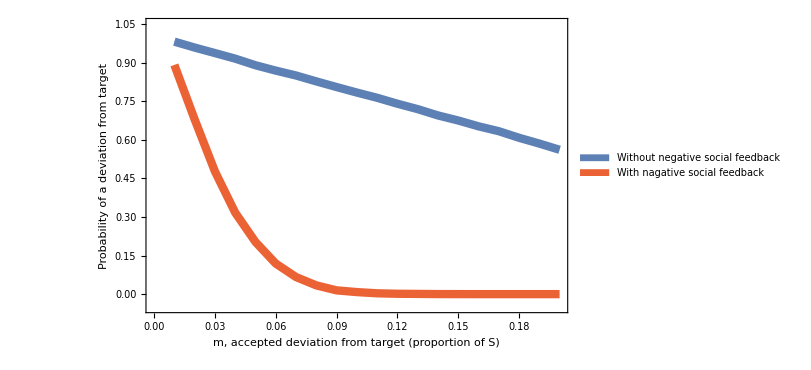

```mathematica
legendSize=20;
axesSize=18;
labelSize=20;

runs=1000;
plt=Show[ListPlot[
{Join[Transpose[{Range[0.01,0.2,0.01]}],Transpose[{Mean[Transpose[Table[Select[marginsTable,#[[3]]==margin&][[All,4]]/runs,{margin,Range[0.01,0.2,0.01]}]]]}],2],
Join[Transpose[{Range[0.01,0.2,0.01]}],Transpose[{Mean[Transpose[Table[Select[marginsTable,#[[3]]==margin&][[All,4]]/runs,{margin,Range[0.01,0.2,0.01]}]]]-1.96StandardDeviation[Transpose[Table[Select[marginsTable,#[[3]]==margin&][[All,4]],{margin,Range[0.01,0.2,0.01]}]]/runs]/Sqrt[runs]}],2],
Join[Transpose[{Range[0.01,0.2,0.01]}],Transpose[{Mean[Transpose[Table[Select[marginsTable,#[[3]]==margin&][[All,4]]/runs,{margin,Range[0.01,0.2,0.01]}]]]+1.96StandardDeviation[Transpose[Table[Select[marginsTable,#[[3]]==margin&][[All,4]],{margin,Range[0.01,0.2,0.01]}]]/runs]/Sqrt[runs]}],2]}
,
PlotStyle->{Directive[colours[[1]],Thickness[0.01]],Directive[colours[[1]],Thickness[0.0]],Directive[colours[[1]],Thickness[0.0]]},
Joined->True,
Filling->{{1->{2}},{1->{3}}},
PlotRange->{-0.05,1.05}
],
ListPlot[
{Join[Transpose[{Range[0.01,0.2,0.01]}],Transpose[{Mean[Transpose[Table[Select[marginsTable,#[[3]]==margin&][[All,5]]/runs,{margin,Range[0.01,0.2,0.01]}]]]}],2],
Join[Transpose[{Range[0.01,0.2,0.01]}],Transpose[{Mean[Transpose[Table[Select[marginsTable,#[[3]]==margin&][[All,5]]/runs,{margin,Range[0.01,0.2,0.01]}]]]-1.96StandardDeviation[Transpose[Table[Select[marginsTable,#[[3]]==margin&][[All,5]],{margin,Range[0.01,0.2,0.01]}]]/runs]/Sqrt[runs]}],2],
Join[Transpose[{Range[0.01,0.2,0.01]}],Transpose[{Mean[Transpose[Table[Select[marginsTable,#[[3]]==margin&][[All,5]]/runs,{margin,Range[0.01,0.2,0.01]}]]]+1.96StandardDeviation[Transpose[Table[Select[marginsTable,#[[3]]==margin&][[All,5]],{margin,Range[0.01,0.2,0.01]}]]/runs]/Sqrt[runs]}],2]}
,
PlotStyle->{Directive[colours[[4]],Thickness[0.01]],Directive[colours[[4]],Thickness[0.0]],Directive[colours[[4]],Thickness[0.0]]},
Joined->True,
Filling->{{1->{2}},{1->{3}}}
],
Frame->True,
FrameStyle->Directive[labelSize],
FrameTicksStyle->axesSize,
FrameLabel->{"m, accepted deviation from target (proportion of S)","Probability of a deviation from target"},
ChartStyle->colours[[2]],
Epilog->Inset[SwatchLegend[{colours[[1]],colours[[4]]},{"Without negative social feedback","With nagative social feedback"},LegendFunction->frame,LabelStyle->legendSize,LegendMarkerSize->20],Scaled[{0.68,0.35}]],
ImageSize->600
]
```